# Lecture 12 Conditioning

We want to be able to estimate what effect small changes in input have on the output in linear algebra problems

Algorithmic implementations always have clear input and output.

Some algorithms have more than one input and/or more than one output.

Since our inputs are vectors and/or matrices there are a variety of ways to measure the perturbation size.

Stability concerns perturbations of the input of an algorithmic implementation. This includes floating point arithmetic!

In an appropriate sense, small input changes produce small output changes for a stable algorithm.

Sometimes it is easier to think of a problem very abstractly as a function f:X→Y

As before some of these functions will have more than one input and/or more than one output. We lump all the inputs together as X  and all the outputs together as Y.

There are various possible measures for perturbation size.

Conditioning concerns perturbations of the input of an abstract function.

The function f is well conditioned at a point x^*∈X if small perturbations in x^* give small perturbations in f(x^*).

An ill-conditioned problem produces large perturbations in f(x^*) for some small perturbation in x^*.

It is possible to have an unstable algorithm for a well-conditioned problem!

## Condition Number

If f is differentiable we can write J(x)=Df(x) then δf=J(x).δx and

#### Absolute Condition Number κ̂ | = | lim_(δ->0) max_(||δx||<δ) (||f(x+δx)-f(x)||)/(||δx||) | = | max_δx (||δf||)/(||δx||)=max_δx (||J(x).δx||)/(||δx||)=||J(x)(||)_induced

#### Relative Condition Number κ | = | lim_(δ->0) sup_(||δx||<δ) (||f(x+δx)-f(x)||/||f(x)||)/(||δx||/||x||) | = | sup_δx (||δf||/||f(x)||)/(||δx||/||x||)=(||J(x)(||)_ind)/(||f(x)||/||x||)

As usual we care more about precision than we do accuracy. Relative condition numbers are much more important than absolute condition numbers!

A problem is well conditioned if k is small (say less than 10^2) and badly conditioned if k is big (say bigger than 10^10).

## Condition Number of f:ℝ→ℝ

We have formulas if f is smooth
	κ̂(x)=sup_δx (||f'(x) δx||)/(||δx||)=|f'(x)|
and 
	κ(x)=sup_δx (||f'(x) δx||/||f(x)||)/(||δx||/||x||)=|f'(x)|×(|x|)/(|f(x)|)

## Condition Number of f:ℝ^n→ℝ^m

We have formulas if f is smooth and we use the Euclidean norms to measure perturbations in the input space ℝ^n and the output space ℝ^m.
	κ̂(x)=sup_δx (||Df(x).δx||)/(||δx||)=sup_δx (||J(x).δx||)/(||δx||)=||J(x)(||)_induced=σ_1
and 
	κ(x)=sup_δx (||Df(x) .δx||/||f(x)||)/(||δx||/||x||)=σ_1×(|x|)/(|f(x)|).

## Condition Number of x→A.x with A∈ℝ^(m×m)

This linear map is smooth. With σ_(1:m) the thick singular values of A and Euclidean norms for the input space ℝ^m and output space ℝ^m we have
	κ̂(x)=σ_1
and 
	κ(x)=σ_1×(||x||)/(||A.x||)≤σ_1×max_(||x||) (||x||)/(||A.x||)=σ_1/σ_m
The condition number of a square matrix is defined to be the ratio of the largest singular value to the smallest singular value.  For A∈ℝ^(m×m) everyone writes 
	K(A)=σ_1/σ_m.
Note if A is not invertible σ_m=0. The condition number of a non-invertible square matrix is ∞.

## Condition Number of solving A.x=b→x with A∈ℝ^(m×m)

This map is smooth with two inputs (A and b) and provided A is invertible we can write it as 
	(A,b)→x=A^-1 b	 
Again write σ_(1:m) for the thick singular values of A and of course use Euclidean norms.

The sensitivity with respect to b is similar to the earlier computation
	(κ̂)_b(A,b)=max(1/σ_(1:m))=1/σ_m
and 
	κ_b(A,b)=1/σ_m×(||b||)/(||A^-1.b||)≤1/σ_m×max_(||b||) (||b||)/(||A^-1.b||)=1/σ_m×1/min[1/σ_(1:m)]=1/σ_m×1/(1/σ_1)=σ_1/σ_m
This is not a typo take a look at the definition and note that 
	κ(A^-1)=κ(A).

Sensitivity with respect to A→A+δA looks slightly different.  We could start from the derivative definitions but we are going to start with the perturbed equation with a fixed b
	(A+δA).(x+δx)=b  
and expand to get
	A.x+δA.x+A.δx+δA.δx=b.
Since A.x=b we have
	  δA.x+A.δx+δA.δx=0
and since δx→0  as δA→0 the quadratic term δA.δx is negligible in the limit and 
	δA.x+A.δx≈0
or in other words 
	δx≈-A^-1.δA.x.
This is all OK because we are considering small perturbations:  it is why we have the limit as δ→0 in our definitions!  When our perturbations are sufficiently small we have
	||δx||≤||A^-1(||)_induced||δA(||)_induced||x||.
There are actually perturbations δA that make ||δx||=||A^-1(||)_induced||δA(||)_induced||x||. If we put this all together we get 
	(||δx||/||x||)/(||δA||/||A||)≤(||A^-1||)/(1/||A||)=||A^-1||||A||=σ_1/σ_m=κ(A)
In other words the relative condition number of solving A.x=b with respect to perturbations δA in A is simply this matrix condition number.

Note: not all condition numbers are simply the ratio of singular values!

## Condition Numbers Matter!

The m×m Hilbert matrix 
	H_(i,j)=1/(i+j-1)
is a symmetric positive definite matrix with a formula for its inverse!  It also has a rapidly growing condition number!

```mathematica
m=6;
H=Table[1/(i+j-1),{i,m},{j,m}];
TabView[{
"H"->MatrixForm[H],
"H^-1"->MatrixForm[Inverse[H]]}]
```

12

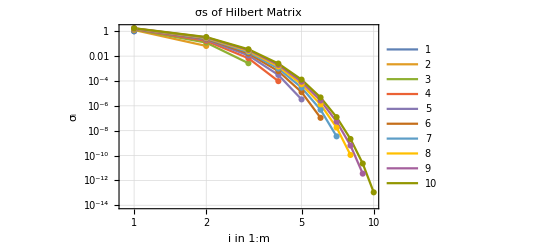

```mathematica
σs=Table[
H=Table[1/(i+j-1),{i,m},{j,m}];
SingularValueList[N[H]],
{m,1,10}];
ListLogLogPlot[σs,
PlotLabel->"σs of Hilbert Matrix",
PlotLegends->Automatic,
Joined->True,Mesh->All,FrameLabel->{"i in 1:m","σ_i"},
Frame->True,GridLines->Automatic]
```

Since the small singular values get tiny the matrices become badly conditioned.  Here is the message and result we get if we try to solve a linear system with a Numerical Hilbert matrix!

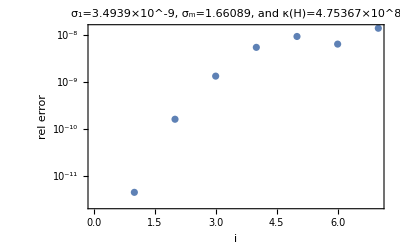

```mathematica
m=7;
H=Table[1/(i+j-1),{i,m},{j,m}];
{σ1,σm}=N[MinMax[SingularValueList[N[H,256]]]];
xIn=RandomInteger[{1,20},m];
b=H.xIn;
xOut=LinearSolve[N[H],b];
ListLogPlot[Abs[(xIn-xOut)/xIn],Frame->True, GridLines->Automatic,
FrameLabel->{"i","rel error"},
PlotLabel->StringForm["σ_1=``, σ_m=``, and κ(H)=``",σ1,σm,σm/σ1]]
```

## Conclusions

You should take such warnings seriously.  The condition number basically tells you the damage (as an error multiplier) that your computation suffers as a result of the linear solve.  If the condition number is 10^6 you have amplified “errors” by 10^6!  The basic double precision round off error starts out at roughly 10^-16 so after using a matrix with condition number 10^6 your new error is roughly 10^-10.  Using such a matrix took you from 16 decimal places to 10 decimal places! Do it again and you lose another six taking you down to an embarrassing 4 decimal places. Do it a third time and your computation is worthless!

## Plan

Wherever possible you should compute with orthogonal matrices Q which satisfy κ(Q)=1 and do not amplify round off errors. If you compute with something other than orthogonal matrices you should try to estimate the condition number and warn users if they could be about to do something stupid.

## Cautionary Example: Wilkerson Polynomial

In your first Linear Algebra class you were taught that you could compute eigenvalues by finding the roots of the characteristic polynomial. The truth is that this is not a good idea because the map from polynomial coefficients to polynomial roots is badly conditioned.

The classic example showing this bad conditioning is the Wilkerson polynomial below.  It turns out that the twitchiest root is the one “near 15” and it is most sensitive to the coefficient of x^15.

```mathematica
W[x_]=Product[(x-i),{i,1,20}];
x/.NSolve[W[x]==0,x]
```

{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.}

The problem lies with the expanded version of W. If you get the coefficients slightly wrong the roots are completely messed up!

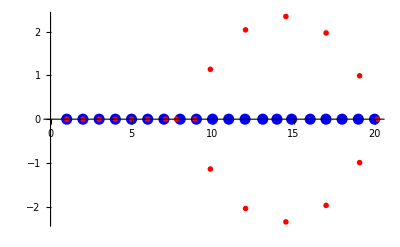

```mathematica
Expand[W[x]];
as=CoefficientList[W[x],x];
bs=as*Table[1+10^-12 RandomReal[{-1,1}],21];
ListPlot[{
ReIm[x/.NSolve[as.Table[x^i,{i,0,20}]==0,x]],ReIm[x/.NSolve[bs.Table[x^i,{i,0,20}]==0,x]]},
PlotStyle->{Directive[PointSize[0.02],Blue],Directive[PointSize[0.01],Red]}]
```

This example means that any attempt to compute eigenvalues by forming the characteristic polynomial is completely misguided.

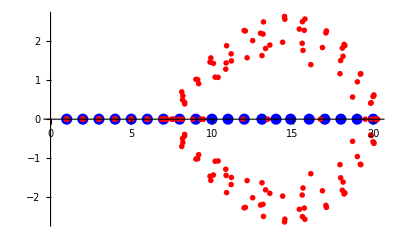

```mathematica
Expand[W[x]];
as=CoefficientList[W[x],x];
MessedUpRoots=ReIm[Flatten[Table[
bs=as*Table[1+10^-12 RandomReal[{-1,1}],21];
x/.NSolve[bs.Table[x^i,{i,0,20}]==0,x],
{10}]]];
ListPlot[{
ReIm[x/.NSolve[as.Table[x^i,{i,0,20}]==0,x]],
MessedUpRoots},
PlotStyle->{Directive[PointSize[0.02],Blue],Directive[PointSize[0.01],Red]}]
```

In fact, the roots of polynomials are frequently found by computing the eigenvalues of a “Companion Matrix”.

```mathematica
m=4;
as=RandomReal[{-1,1},m];
vars=Table[x^i,{i,0,m-1}];
p[x_]=x^m+as.vars;
x/.NSolve[p[x]==0,x]
A=SparseArray[{
Band[{2,1}]->1,
Band[{1,m},{m,m},{1,0}]->-as
},
{m,m}];
Eigenvalues[A]
```

{-0.770743,-0.0870698,0.395409-0.923669 ⅈ,0.395409+0.923669 ⅈ}

{0.395409+0.923669 ⅈ,0.395409-0.923669 ⅈ,-0.770743+0. ⅈ,-0.0870698+0. ⅈ}

# Lecture 13 Floating Point Arithmetic

The question is how do computers do arithmetic?

The answer used to be lots of different ways.

This was bad for a lot of reasons.

The answer now is carefully and consistently with a detailed set of specifications called  IEE 754

Created by the IEEE in 1985 and updated in 2008  https://en.wikipedia.org/wiki/IEEE_754

Three standard computational precisions:

FP64 aka Double Precision

FP32 aka Single Precision

FP16 aka Half Precision

FP stands for floating point and indicates that numbers are considered in scientific notation

significand×base^exponent

In base 10  π^E≈2.24592 ×10^1. The exponent 1 has floated the decimal point to just after the first position!

## Decimal, Hexadecimal, and Binary Representations

### Decimal

Presumably because we have 10 fingers we learn to count in base 10.  Decimal numbers use the symbols 
	0,1,2,3,4,5,6,7,8,9
to encode integers. Early in our arithmetic classes we learned that
	2345 means 5*10^0+4*10^1+3*10^2+2*10^4.
Slightly later we learn that 
	23.45 means 5*10^-2+4*10^-1+3*10^0+2*10^1
We do not indicate the base because base 10 is the default.

### Hexadecimal

The Bane https://en.wikipedia.org/wiki/Invasion_of_the_Bane have 16 lesser tentacles and use base 16. Dr Who  has translated their digits into the symbols
	0,1,2,3,4,5,6,7,8,9,a,b,c,d,e,f
where a=10, b=11, c=12, d=13, e=14, f=15.  Of course we do not need a symbol for 16 because 
	10_16=0+1*16=16
Non decimal bases are represented by subscripts.  base 16 is called Hex! Naturally the Bane use Hexadecimal fractions and write them as “Heximals”. For instance “bc.1df” is 11*16+12+1*16^-1+13*16^-2+15*16^-3.  
Computers understand hexadecimal integers.

```mathematica
HexStrings=Map[IntegerString[#,16]&,{16,2345,967,31}]
Map[FromDigits[#,16]&,HexStrings]
```

{10,929,3c7,1f}

{16,2345,967,31}

They also can compute and understand and convert between “heximals”.

```mathematica
OldFrac=19/17;
{base,digits}={16,23};
HexStuff=RealDigits[OldFrac,base,digits]
NewFrac=FromDigits[HexStuff,base]
N[{OldFrac,NewFrac},32]
```

{{1,1,14,1,14,1,14,1,14,1,14,1,14,1,14,1,14,1,14,1,14,1,14},1}

172947505488398714875612943/154742504910672534362390528

{1.1176470588235294117647058823529,1.1176470588235294117647058819728}

### Binary

The Bynars https://en.wikipedia.org/wiki/11001001 count in base 2. They only have two symbols
	0,1
The Star Trek episode title is 
	11001001_2=1*2^7+1*2^6+0*2^5+0*2^4+1*2^3+0*2^2+0*2^1+1*2^0=201 
“Binamals” work exactly the same way as “hexamils”

```mathematica
FromDigits["11001001",2]
OldFrac=19/17;
{base,digits}={2,23};
HexStuff=RealDigits[OldFrac,base,digits]
NewFrac=FromDigits[HexStuff,base]
N[{OldFrac,NewFrac},32]
```

201

{{1,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1},1}

4687751/4194304

{1.1176470588235294117647058823529,1.1176469326019287109375}

## Computer Representation

### Computer Organization

In the past, people have imagined and made ternary computers https://en.wikipedia.org/wiki/Ternary_computer. One common way to talk about the memory states for such a thing would be -1,0,1.

However, modern computer memory is just a bunch of switches either on or off. Modern computers are naturally binary and folks talk about the states as zeros and ones. Each switch is called a bit and they are organized into groups of 8 called a byte.  So a byte is 8 bits
	 b_1 | b_2 | b_3 | b_4 | b_5 | b_6 | b_7 | b_8
All 8 bits zero is zero as an integer.  All 8 bits one is 255 as an integer.  This explains the choice of 0-255 grayscale for the crudest historical grayscale images: Each pixel was a single byte.  Of course, a black and white image can be stored with a single bit for each pixel!

Bytes are organized into computer words.  Historical computers used a variety of word lengths   
https://en.wikipedia.org/wiki/Word_(computer_architecture)#Word_size_choice
Relatively modern computers all used to have a word length of 32 bits or equivalently 4 bytes.  Almost all modern computing devices have word lengths of 64 bits or 8 bytes.  Graphical Programming Units and equivalent numerical co-processors can usefully treat a 64 bit word as four sets of 16 bits!     Not surprisingly:

FP16 is a floating point number occupying 16 bits. Called Half precision

FP32 is a floating point number occupying 32 bits. Called Single precision

FP64 is a floating point number occupying 64 bits. Called Double precision

Also not surprisingly, the larger representations are more accurate and cover a greater range. With a limited number of bits there is a trade of between range and accuracy.  Most computations are done in FP64 these days.  In data science a surprising and growing fraction of computations are being done in FP16.

### Floating Point Specifications

The floating point representations all look like
	(±1)×2^p×("1.xxx…xx")_2
They differ in the number of bits set aside for the exponent p and the significand ("1.xxx…xx")_2.

Roughly speaking: Single precision (FP32) is what scientists and engineers thought they wanted (six or seven significant decimal digits); Double Precision was invented to help get six or seven decimal digits in answers; then Half precision (FP16) was formalized when game designers and data scientists realized that they needed lots of arithmetic much more than they needed six or seven accurate digits.

As a practical matter unless you are very computing things on specialized (or weird) hardware you are using the default machine arithmetic on your computer.  Unless you are on a GPU or something like a fridge you are computing in FP64 and people report answers to what is essentially FP32. Our target is to understand the following output.

```mathematica
{$MachineEpsilon,N[2^-52]}
N[π]
```

{2.22045×10^-16,2.22045×10^-16}

3.14159

Details of the three common formats follow.

#### FP16

The specification says there is:

1 sign bit interpreted as ±

5 exponent bits interpreted as the power p in 2^p

"11111" is reserved for as big as possible i.e. ±∞

"00000" is reserved for as small as possible i.e. ±0 and tiny denormalized numbers.

There are 30=2^5-2 remaining bit patterns they are interpreted as 
	2^(-15 +  (e_1 | e_2 | e_3 | e_4 | e_5)_2)
The offset 15 is chosen to split the difference between big and small.  The exponent range is 
	-15 +  (0 | 0 | 0 | 0 | 1)_2=-14≤p≤ 15= -15 +  (0 | 1 | 1 | 1 | 1)_2

The 10 significand bits b_1,b_2,…,b_10 are interpreted as
	 (1 | . | b_1 | b_2 | b_3 | b_4 | b_5 | b_6 | b_7 | b_8 | b_9 | b_10)_2 
unless the exponent is "00000" or "11111"

This is a normalized floating point number and has 10 specified binary bits

The smallest positive normalized floating point number is 2^-14×1≈"6.10352"×10^("-5") all the binary bits are significant.

The largest positive floating point number is 2^15×(2-2^-10)≈"6.5504"×10^("4")

If the the exponent is "00000" the significand is interpreted as 	
	(0 | . | b_1 | b_2 | b_3 | b_4 | b_5 | b_6 | b_7 | b_8 | b_9 | b_10)_2

This is a denormalized or subnormal floating point number.

The smallest positive denormalized number is 2^-14×("0.0000000001")_2=2^-14×2^-10≈5.96×10^-8. It only has one significant binary bit.

If the exponent is "11111"

If b_1=b_2=…=b_10=0 we have ±∞.

If they are not all zero it is a flavor of “NaN”  (error form standing for Not A Number).  For a summary see https://en.wikipedia.org/wiki/NaN. For details look at the technical specification!

To convert a real number to a normalized FP16 it has to be rounded to the appropriate number of binary bits
	 (1 | . | b_1 | b_2 | b_3 | b_4 | b_5 | b_6 | b_7 | b_8 | b_9 | b_10 | ? | ? | ? | ?)_2 
The ? are either thrown away or not computed.  The first ? (the one in the slot that would be b_11) is either a zero or a one and represents  ?*2^-11.

If we worry about relative error this first missing digit could represent an error of 2^-11 in a value between 1 and 2.  Since 2^-11≈"4.88281"×10^("-4") this is about three significant decimal digits.  A careful way to say this is to report the largest positive number ϵ that satisfies (1.0 + ϵ = 1.0)_FP16 in FP16 arithmetic. With this definition 
	ϵ_16=(0 | . | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | …)_2=2^-10 ≈"9.76563"×10^("-4")

#### FP32

The specification says there is:

1 sign bit interpreted as ±

8 exponent bits interpreted as the power p in 2^p

"11…11" is reserved for as big as possible i.e. ±∞

"00…00" is reserved for as small as possible i.e. ±0 and tiny denormalized numbers.

The bit patterns are interpreted as 
	2^(-127 +  (e_1 | e_2 | … | e_7 | e_8)_2)
The offset 127 gives the exponent range is 
	-126≤p≤ 127

The 23 significand bits b_1,b_2,…,b_10 are interpreted as
	 (1 | . | b_1 | b_2 | … | b_22 | b_23)_2 
unless the exponent is "00…00" or "11…11"

This is a normalized floating point number and has 23 specified binary bits

The smallest positive normalized floating point number is 2^-126×1≈"1.17549"×10^("-38") all the binary bits are significant.

The largest positive floating point number is 2^127×(2-2^-24)≈"3.40282"×10^("38")

If the the exponent is "00…00" the significand is interpreted as 	
	(0 | . | b_1 | b_2 | … | b_22 | b_23)_2

This is a denormalized or subnormal floating point number.

The smallest positive denormalized number is 2^-126×2^-23≈"1.4013"×10^("-45"). It only has one significant binary bit.

If the exponent is "11…11"

If b_1=b_2=…=b_23=0 we have ±∞.

If they are not all zero it is a flavor of “NaN”  (error form standing for Not A Number).  For a summary see https://en.wikipedia.org/wiki/NaN. For details look at the technical specification!

The largest positive number satisfying (1.0 + ϵ = 1.0)_FP32 is ϵ_32=2^-23≈"1.19209"×10^("-7")  So FP32 has roughly 7 decimal digits of precision.

#### FP64

The specification says there is:

1 sign bit interpreted as ±

11 exponent bits interpreted as the power p in 2^p

"11…11" is reserved for as big as possible i.e. ±∞

"00…00" is reserved for as small as possible i.e. ±0 and tiny denormalized numbers.

The bit patterns are interpreted as 
	2^(-1023 +  (e_1 | e_2 | … | e_10 | e_11)_2)
The offset 1023 gives the exponent range is 
	-1022≤p≤ =1023

The 52 significand bits b_1,b_2,…,b_52 are interpreted as
	 (1 | . | b_1 | b_2 | … | b_51 | b_52)_2 
unless the exponent is "00…00" or "11…11"

This is a normalized floating point number and has 52 specified binary bits

The smallest positive normalized floating point number is 2^-1022×1≈"2.22507"×10^("-308")

The largest positive floating point number is 2^1023×(2-2^-52)≈"1.79769"×10^("308")

If the the exponent is "00…00" the significand is interpreted as 	
	(0 | . | b_1 | b_2 | … | b_51 | b_52)_2

This is a denormalized or subnormal floating point number.

The smallest positive denormalized number is 2^-1022×2^-52≈"4.94066"×10^("-324")

If the exponent is "11…11"

If b_1=b_2=…=b_52=0 we have ±∞.

If they are not all zero it is a flavor of “NaN”  (error form standing for Not A Number).  For a summary see https://en.wikipedia.org/wiki/NaN. For details look at the technical specification!

The largest positive number satisfying (1.0 + ϵ = 1.0)_FP64 is ϵ_64=2*2^-53≈2*"1.11022"×10^("-16")  So FP64 has roughly 15 decimal digits of precision.

```mathematica
$MachinePrecision
$MachineEpsilon
```

15.9546

2.22045×10^-16

## Floating Point Axioms

All the arithmetic (and some other things) are correctly rounded in IEEE compliant arithmetic.

Every compliant floating point operation is exact 
up to a relative error of size at most ϵ_machine!

Compliant operations include:  +,-,×,÷,√, 1/√,…

In practice basic math functions (sin, cos, atan, …) which are part of the distribution are compliant over reduced ranges.

```mathematica
a1=123456.1;
a2=123456.2;
Abs[a1-a2]
Abs[a1-a2]/a1
```

0.1

8.10005×10^-7

```mathematica
p=23;
Normal[Series[Sin[t],{t, 0, p}]]
Normal[Series[Cos[t],{t, 0, p}]]
f[t_]=Normal[Series[Exp[t],{t, 0, p}]]
```

t-t^3/6+t^5/120-t^7/5040+t^9/362880-t^11/39916800+t^13/6227020800-t^15/1307674368000+t^17/355687428096000-t^19/121645100408832000+t^21/51090942171709440000-t^23/25852016738884976640000

1-t^2/2+t^4/24-t^6/720+t^8/40320-t^10/3628800+t^12/479001600-t^14/87178291200+t^16/20922789888000-t^18/6402373705728000+t^20/2432902008176640000-t^22/1124000727777607680000

1+t+t^2/2+t^3/6+t^4/24+t^5/120+t^6/720+t^7/5040+t^8/40320+t^9/362880+t^10/3628800+t^11/39916800+t^12/479001600+t^13/6227020800+t^14/87178291200+t^15/1307674368000+t^16/20922789888000+t^17/355687428096000+t^18/6402373705728000+t^19/121645100408832000+t^20/2432902008176640000+t^21/51090942171709440000+t^22/1124000727777607680000+t^23/25852016738884976640000

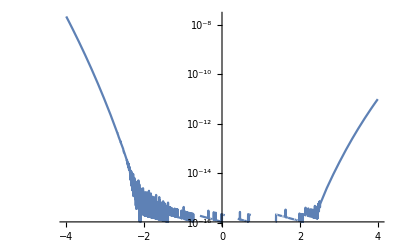

```mathematica
LogPlot[Abs[(f[t]-Exp[t])/Exp[t]],{t, -4,4},
PlotRange->All]
```

# Lecture 12 Summary

The relative condition number of a smooth problem f:X→Y at x∈X is κ=(||J(x)(||)_ind)/(||f(x)||/||x||) where J(x)=Df(x).

The condition number of f:X→Y at x∈X tells you the relative sensitivity of the output y=f(x) to relative perturbations in the input x.

The condition number of an m×m square matrix A is the ratio of the largest and smallest singular values κ(A)=σ_1/σ_m.

κ(A) is the condition number for both x→A x  and (A,b)->A^-1 b

If I know x to 16 significant decimals then I can only compute A x to 16-log_10(k(A))

Any time I do anything with a matrix A I lose log_10(κ(A)) decimal places.

# Lecture 13 Summary

Double precision arithmetic starts with ∼16 decimal places.

If x is double precision and κ(A)~10^10 then A x only has six decimal places left.

If A is double precision and κ(A)~10^12 then A^-1 b only has 4 decimal places left.

From now on x̃ is an approximation to x and f̃is an approximation to f etc.

# Lecture 14 Stability

This is going to look a bit abstract for a couple of lectures!

Definition of Accuracy.

Definition of  Stability.

Importance of Backwards stability.

We are back to thinking about small perturbations but now in practical algorithms in floating point arithmetic.

## Big “O” meaning: ϕ(t)=O(ψ(t))

ϕ(t)=O(ψ(t)) as t→0 means there is a “constant” C satisfying

||ϕ(t)||≤C ψ(t)  as t→0.

For t→∞ etc make the obvious substitutions

This is a standard math definition

There are a bunch of more complicated but similar ideas https://en.wikipedia.org/wiki/Big_O_notation used in CS etc.

## Big “O” meaning in NLA: O(ϵ_machine)

O(ϵ_machine) means we imagine repeating a computation with increasing precision and hence decreasing ϵ! It means we think about letting ϵ→0!

In practice all we can really do is Half, Single, Double, … https://en.wikipedia.org/wiki/Machine_epsilon  i.e.

Half-FP16 has ϵ roughly 10^-4

Single-FP32 has ϵ roughly 10^-7

Double-FP64 has ϵ roughly 10^-16

(available on some computers) Quad-FP128 has ϵ roughly 10^-35

(available on some computers) Oct-FP256 has ϵ roughly 10^-69

So what does ||□||=O(ϵ_machine) mean for an algorithm f̃:X→Y mean?

It means that there is a constant C (good for all inputs X) theoretically satisfies ||□||<C ϵ as ϵ→0.

In NLA the input space X always means a fixed dimension.

The constant can depend on m and n.

## Typical Result: Linear solve i.e. A.x=b→x̃

For A∈ℝ^(m×m) the expression (||x-x̃||)/(||x||)=O(κ(A) ϵ_machine) means

||x-x̃||≤||x||C κ(A) ϵ_machine on any sufficiently accurate machine for every A and b.

Remember, we know how to compute κ(A)=||A||/||A^-1||=σ_1/σ_m

## Accuracy

We have an abstract problem f:X→Y with a floating point algorithm f̃:X→Y.

The algorithm is accurate if  (|| f̃(x) - f(x) ||)/(||f(x)||)=O(ϵ_machine)

In words: “An accurate algorithm gives nearly the right answer!”

## Stability

We have an abstract problem f:X→Y with a floating point algorithm f̃:X→Y.

The algorithm is stable if  (|| f̃(x) - f(x̃) ||)/(||f(x̃)||)=O(ϵ_machine) for some x̃ satisfying(|| x - x̃ ||)/(||x||)=O(ϵ_machine)

In words: “A stable algorithm gives nearly the right answer to nearly the right question!”

## Backward Stability

We have an abstract problem f:X→Y with a floating point algorithm f̃:X→Y.

The algorithm is backwards stable if  f̃(x) = f(x̃) for some x̃ satisfying(|| x - x̃ ||)/(||x||)=O(ϵ_machine)

In words: “A backwards stable algorithm gives exactly the right answer to nearly the right question!”

## Norms

In finite dimensions (like we are) all norms are equivalent in the sense that 
	c_1||□(||)_1≤||□(||)_2≤c_2||□(||)_1
for some constants 0<c_1≤c_2<∞.  This means that our definitions do not depend what norm we use!

# Lecture15 Stability (cont)

Still looking a bit abstract for one more lecture!

## Algorithm 17.1: R.x=b⟶x

### Manual To Start!

We want to solve the triangular system R.x=b where R is a square upper triangular matrix!

```mathematica
Clear[x]
m=4;
R=UpperTriangularize[RandomReal[{-1,1},{m,m}]];
ans = Array[x,m];
b=RandomReal[{-1,1},m];
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
x[2]
x[3]
x[4]),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. The last row gives the last value in the answer!

```mathematica
ans⟦-1⟧=b⟦-1⟧/R⟦-1,-1⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
x[2]
x[3]
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. Once you know the last value in the answer the second last row gives the second last value in the answer.

```mathematica
ans⟦-2⟧=(b⟦-2⟧-R⟦-2,-1⟧*ans⟦-1⟧)/R⟦-2,-2⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
x[2]
-0.00818474
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. Once you know the last two values in the answer the third last row gives the third last value in the answer.

```mathematica
ans⟦-3⟧=(b⟦-3⟧-R⟦-3,-2;;-1⟧.ans⟦-2;;-1⟧)/R⟦-3,-3⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
-1.53782
-0.00818474
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. Once you know the last three values in the answer the 4th last row gives the 4th last value in the answer.

```mathematica
ans⟦-4⟧=(b⟦-4⟧-R⟦-4,-3;;-1⟧.ans⟦-3;;-1⟧)/R⟦-4,-4⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(0.510183
-1.53782
-0.00818474
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Looks as though we are done!  We should check we did not mess up!

```mathematica
R.ans-b
```

{1.11022×10^-16,1.11022×10^-16,0.,0.}

### Script

We want to solve the triangular system R.x=b where R is a square upper triangular matrix!  Here is a script.

```mathematica
Clear[x]
m=7;
R=UpperTriangularize[RandomReal[{-1,1},{m,m}]];
MatrixPlot[R,Mesh->All];
b=RandomReal[{-1,1},m];
ans=ConstantArray[0,m];
Do[
ans⟦i⟧=(b⟦i⟧-R⟦i,i+1;;m⟧.ans⟦i+1;;m⟧)/R⟦i,i⟧,
{i,m,1,-1}]
Norm[R.ans-b]
```

1.27192×10^-15

### Function

We want to solve the triangular system R.x=b where R is a square upper triangular matrix!  Here is a script.

```mathematica
Clear[AASUTSolve]
AASUTSolve[R_,b_]:= Module[{m=Length[b],x},
(* Alg 17.1 No checking *)
x=ConstantArray[0,m];
Do[
x⟦i⟧=(b⟦i⟧-R⟦i,i+1;;m⟧.x⟦i+1;;m⟧)/R⟦i,i⟧,
{i,m,1,-1}];
x]
```

Testing!

```mathematica
m=34;
R=UpperTriangularize[RandomReal[{-1,1},{m,m}]];
b=RandomReal[{-1,1},m];
x=AASUTSolve[R,b];
Norm[R.x-b]
```

4.33373×10^-8

```mathematica
Diagonal[R]
```

{0.309743,-0.199917,-0.256743,-0.735726,-0.215098,-0.859207,0.256306,0.158967,0.910289,-0.354942,-0.909153,-0.150743,0.460218,0.312975,-0.273728,0.228468,-0.700538,-0.645497,0.21604,-0.32615,-0.987589,0.886581,0.636952,-0.29175,0.271177,0.0230517,-0.746463,-0.988451,0.730044,0.0412965,-0.49885,-0.124322,0.591325,-0.422252}

## Accuracy/Stability/Backwards Stability

We have an abstract problem f:X→Y with a floating point algorithm f̃:X→Y.

f̃ is accurate if  (|| f̃(x) - f(x) ||)/(||f(x)||)=O(ϵ_mac): 
"Accurate algorithms give nearly the right answer!"

f̃ is stable if  (|| f̃(x) - f(x̃) ||)/(||f(x̃)||)=O(ϵ_machine) for x̃ with (|| x - x̃ ||)/(||x||)=O(ϵ_mac): 
"Stable algorithms give nearly the right answer to nearly the right question!"

f̃ is backwards stable if  f̃(x) = f(x̃) for some x̃ satisfying(|| x - x̃ ||)/(||x||)=O(ϵ_machine) 
“Backwards stable algorithm give the right answer to nearly the right question!”

## Floating Point Ops: +, -, ×, ÷, … are backwards stable

This is going to look a bit “picky”!

Let X=ℝ^2 and write X={x_1,x_2}∈X.  Note, x_1 and x_2 are probably not representable floating point numbers. For instance hey could be π or or e or 1/10.

Approximate by floating point numbers i.e.  (x̃)_1=fl(x_1) and (x̃)_2=fl(x_2).  Remember by our floating point axioms (x̃)_1=x_1(1+ϵ_1) and (x̃)_2=x_2(1+ϵ_2) with both ϵ_1 and ϵ_2 less than ϵ_machine.

### FP Subtraction

FP subtract “⊖” the FP numbers and remember that (x̃)_1⊖(x̃)_2=((x̃)_1-(x̃)_2)(1+ϵ_3)

Combine the bits together  (x̃)_1⊖(x̃)_2=((x̃)_1-(x̃)_2)(1+ϵ_3)=(x_1(1+ϵ_1)-x_2(1+ϵ_2))(1+ϵ_3)

Multiply them all out (x̃)_1⊖(x̃)_2=x_1(1+ϵ_1)(1+ϵ_3)-x_2(1+ϵ_2)(1+ϵ_3)=x_1(1+ϵ_4)-x_2(1+ϵ_5) where ϵ_4=ϵ_1+ϵ_3+ϵ_1 ϵ_3 etc.

Note that |ϵ_4|≤2 ϵ_machine+O(ϵ_machine^2) with the same statement for ϵ_5.

Squint at at this a bit and you see we have all the pieces for backward stability.  We can take C=3.

### Other FP Ops

They all work the same: use the representation; work through the arithmetic; and collect stuff up at the end.

## Examples: Talk about the book examples p109-11

## Wilkinson Polynomial and Eigen Values!

Root finding for polynomials is twitchy. Consider the following “twitchy” polynomial with obvious roots. For some background see https://en.wikipedia.org/wiki/Wilkinson%27s_polynomial

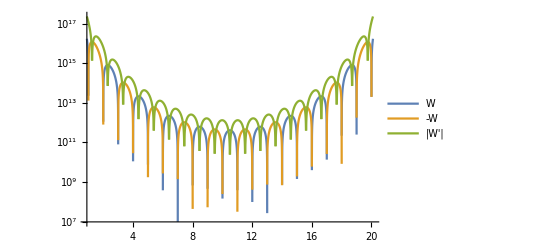

```mathematica
WilkinsonPoly[n_][x_]:=Product[(x-i),{i,1.0,n}]
n=20;
LogPlot[ {WilkinsonPoly[n][x],-WilkinsonPoly[n][x],Abs[WilkinsonPoly[n]'[x]]},{x,0.9,n+0.1},
PlotLegends->{"W","-W","|W'|"}]
```

If I mess with the coefficients just a tiny bit it goes nuts for relatively small n

```mathematica
WilkinsonPoly[17][x]//Expand
```

-3.55687×10^14+1.22341×10^15 x-1.8216×10^15 x^2+1.58331×10^15 x^3-9.093×10^14 x^4+3.69013×10^14 x^5-1.10228×10^14 x^6+2.48718×10^13 x^7-4.30811×10^12 x^8+5.77925×10^11 x^9-6.02027×10^10 x^10+4.85322×10^9 x^11-2.99651×10^8 x^12+1.38966×10^7 x^13-468180. x^14+10812. x^15-153. x^16+x^17

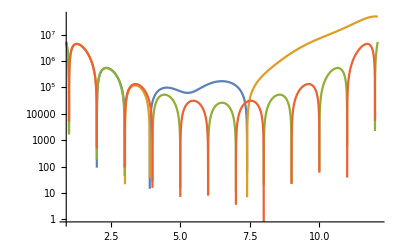

```mathematica
n=12;ϵ=10^-7;
as=CoefficientList[WilkinsonPoly[n][x],x];
bs = as*RandomReal[{1-ϵ,1+ϵ},n+1];
p[cs_][x_]:= Sum[cs[[i]] x^(i-1),{i,Length[cs]}]
LogPlot[ {p[bs][x],-p[bs][x],p[as][x],-p[as][x]},{x,0.9,n+0.1}]
```

The moral of this story is that you can not compute anything that uses the coefficients of even a moderate degree polynomial.

In particular, you can not compute eigenvalues by constructing the characteristic polynomial!

In fact, you can (and matlab does) compute polynomial roots by building a matrix!

## Backward Stability and Accuracy

We have an abstract problem f:X→Y with a floating point algorithm f̃:X→Y.

f̃ is accurate if  (|| f̃(x) - f(x) ||)/(||f(x)||)=O(ϵ_mac): 
"Accurate algorithms give nearly the right answer!"

f̃ is backwards stable if  f̃(x) = f(x̃)  for some x̃ satisfying(|| x - x̃ ||)/(||x||)=O(ϵ_machine) 
“Backwards stable algorithm give the right answer to nearly the right question!”

The condition number of f at x∈X is the inherent sensitivity κ(x) of the problem

Theorem 15.1: A backwards stable algorithm f̃ gives relative error O(κ(x)ϵ_machine)
	In symbols,  (|| f̃(x) - f(x) ||)/(||f(x)||)=O(κ(x)ϵ_machine).	
	In practice, the condition number reduces the precision.

This is pretty much exactly what we “think” should happen.

We have a computable "difficulty" for the problem instance "compute f(x)”.  This is the condition number κ(x). It reduces the relative precision of our answer in a predictable way.

For lots of problems the hidden constant in the “bigO” is O(1). In this case log_10 κ(x) is roughly how many decimal digits you lose.

### Work the Proof

# Lecture 16 Stability of Householder QR

The plan is to look at Householder QR with our new tool.

f̃ is backwards stable if  f̃(x)=f(x̃) for some x̃ satisfying(|| x - x̃ ||)/(||x||)=O(ϵ_machine) 
“Backwards stable algorithm give the right answer to nearly the right question!”

Theorem 15.1 if f̃ is a backwards stable algorithm then (|| f̃(x) - f(x) ||)/(||f(x)||)=O(κ(x)ϵ_machine)

## Understanding QR Behavior

We need to think if it is a thin Q, or fat Q , or neither is part of the output.  Maybe, we should think of the vectors (v_i) that define both matrices Q as output.  Maybe we just throw the rotations away!

### A→{Q,R}

As we have seen the built in Householder QR in all our tools produces exactly upper triangular Rs and almost orthogonal matrices Q that almost satisfy A=Q.R.  Mathematica is annoying because it gives us the Q on it side!

{1.13851×10^-15,3.7447×10^-15,9.03221}

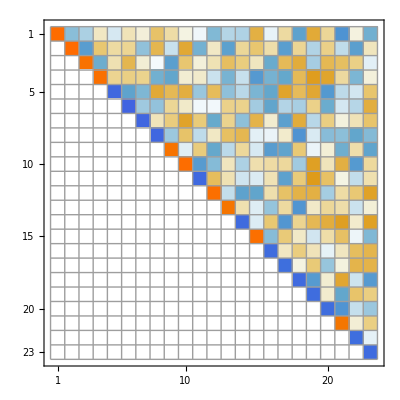

```mathematica
{m,n}={123,23};
A=RandomReal[{-1,1},{m,n}];
{Q,R}=QRDecomposition[A]; Q=Qᵀ;
Map[Norm,{Qᵀ.Q-IdentityMatrix[n],A-Q.R,A}]
MatrixPlot[R,Mesh->All]
```

### {Q_1,R_1}→Q_1.R_1=A→{Q_2,R_2}

The question now is how twitchy is the process.

```mathematica
{m,n}={252,25};
R1=UpperTriangularize[RandomReal[{-1,1},{n,n}]];
Q1=QRDecomposition[RandomReal[{-1,1},{m,n}]]⟦1⟧ᵀ;
A=Q1.R1; {Q2,R2}=QRDecomposition[A];Q2=Q2ᵀ;
TabView[{"R1"->MatrixPlot[R1,Mesh->All],"R2"->MatrixPlot[R2,Mesh->All]}];
TableForm[
Map[Norm,{A,A-Q1.R1,A-Q2.R2,Q1ᵀ.Q1-IdentityMatrix[n],Q2ᵀ.Q2-IdentityMatrix[n],R1-R2,Q1-Q2}],
TableHeadings->{{"||A||","res_1","res_2","orth_1","orth_2","||R1-R2||","||Q1-Q2||"}}]
```

||A|| | 4.1406
res_1 | 0.
res_2 | 2.43693×10^-15
orth_1 | 8.39114×10^-16
orth_2 | 1.3579×10^-15
||R1-R2|| | 6.09711×10^-11
||Q1-Q2|| | 4.57978×10^-10

What this means is that both the decompositions work but that they are not really all that similar! This means that the forward problem is ill-conditioned aka “twitchy”.  The product is stable but the bits (multiplicands) are not!
	As a bad analogy suppose I ask you to try to guess the numbers x and y from the product x*y.

## Backward Stability of Householder QR

What we have is that multiplying the factors gives something close to the input.  In other words we have
	A→{Q,R}→Q.OverTilde[R=A+δA]
with δA relatively small.

Remember how our Householder computation went.  We started with a Tall-Skinny m×n matrix A_0 and computed a v_1 (using +, ×, √□, and ÷) that implicitly defined in exact arithmetic an exactly orthogonal Q_1=I_m-2 v_1⊗v_1which gave 
	A_1=Q_1.A_0
and all the arithmetic to make v_1 was to make A_1 have all the entries below the first exactly equal to zero.  Note, the condition number of Q_1 is as small as possible i.e. κ(Q_1)=1.  The condition number of (Q̃)_1 (the computed Q_1) is just a smidge bigger with κ((Q̃)_1)=1+ϵ_1with ϵ_1=O(ϵ_machine).  We continue with the next column and accumulate the product of all these Q_i until we are left with R. This finite sequence of actions are with matrices with condition number 1+O(ϵ_machine).  The result is a decomposition satisfying
	Q̃.R̃=A+δA  with (||δA||)/(||A||)=O(ϵ_machine)

## Combining Backward Stable Steps

If all steps of an algorithm are backwards stable then the algorithm is backward stable.

## A.x=b⟶Q.R.x=b⟶R.x=Qᵀ.b⟶x

Solving a linear system using the QR decomposition is backwards stable.

We know all the steps except the upper triangular linear solve are backwards stable.  We are going to look at the triangular solve (algorithm 17.1) right after we implement this

```mathematica
m=22;
x = RandomReal[{-1,1},m];
A=RandomReal[{-1,1},{m,m}];
b=A.x;
{Q,R}=QRDecomposition[A];Q=Qᵀ;
xHat=LinearSolve[R,Qᵀ.b];
Norm[x-xHat]
```

3.00611×10^-15

What we need to do is build a nearby problem that xHat solves exactly.  We are thinking of A as the data in Theorem 16.2 (in other words we can not mess with b right now) so we want to find a relatively small modification ΔA to A so that
	(A+ΔA).xHat=b
We know almost everything in this recipe except ΔA!  Rearrange to have
	ΔA.xHat=b-A.xHat
There are lots of possible choices! I can choose the rank one modification 
	ΔA=(b-A.xHat)⊗xHat/(||xHat||)
which has induced two norm ||ΔA||=||b-A.xHat||.

## Algorithm 17.1: R.x=b⟶x Manual To Start!

We want to solve the triangular system R.x=b where R is a square upper triangular matrix!

```mathematica
Clear[x]
m=4;
R=UpperTriangularize[RandomReal[{-1,1},{m,m}]];
ans = Array[x,m];
b=RandomReal[{-1,1},m];
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
x[2]
x[3]
x[4]),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. The last row gives the last value in the answer!

```mathematica
ans⟦-1⟧=b⟦-1⟧/R⟦-1,-1⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
x[2]
x[3]
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. Once you know the last value in the answer the second last row gives the second last value in the answer.

```mathematica
ans⟦-2⟧=(b⟦-2⟧-R⟦-2,-1⟧*ans⟦-1⟧)/R⟦-2,-2⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
x[2]
-0.00818474
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. Once you know the last two values in the answer the third last row gives the third last value in the answer.

```mathematica
ans⟦-3⟧=(b⟦-3⟧-R⟦-3,-2;;-1⟧.ans⟦-2;;-1⟧)/R⟦-3,-3⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
-1.53782
-0.00818474
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. Once you know the last three values in the answer the 4th last row gives the 4th last value in the answer.

```mathematica
ans⟦-4⟧=(b⟦-4⟧-R⟦-4,-3;;-1⟧.ans⟦-3;;-1⟧)/R⟦-4,-4⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(0.510183
-1.53782
-0.00818474
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Looks as though we are done!  We should check we did not mess up!

```mathematica
R.ans-b
```

{1.11022×10^-16,1.11022×10^-16,0.,0.}

## Algorithm 17.1: R.x=b⟶x Script

We want to solve the triangular system R.x=b where R is a square upper triangular matrix!  Here is a script.

```mathematica
Clear[x]
m=7;
R=UpperTriangularize[RandomReal[{-1,1},{m,m}]];
MatrixPlot[R,Mesh->All];
b=RandomReal[{-1,1},m];
ans=ConstantArray[0,m];
Do[
ans⟦i⟧=(b⟦i⟧-R⟦i,i+1;;m⟧.ans⟦i+1;;m⟧)/R⟦i,i⟧,
{i,m,1,-1}]
Norm[R.ans-b]
```

1.27192×10^-15

## Algorithm 17.1: R.x=b⟶x Function

We want to solve the triangular system R.x=b where R is a square upper triangular matrix!  Here is a script.

```mathematica
Clear[AASUTSolve]
AASUTSolve[R_,b_]:= Module[{m=Length[b],x},
(* Alg 17.1 No checking *)
x=ConstantArray[0,m];
Do[
x⟦i⟧=(b⟦i⟧-R⟦i,i+1;;m⟧.x⟦i+1;;m⟧)/R⟦i,i⟧,
{i,m,1,-1}];
x]
```

Testing!

```mathematica
m=7;
R=UpperTriangularize[RandomReal[{0.1,10},{m,m}]];
b=RandomReal[{-1,1},m];
x=AASUTSolve[R,b];
Norm[R.x-b]
```

1.16441×10^-15